# Square

### Author

Eric W. Weisstein
August 27, 2010

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polygons/Square.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Square.html.

©2010 Wolfram Research, Inc. except for portions noted otherwise

## Graphic

```mathematica
Show[Graphics[RegularPolygon[4],AspectRatio->Automatic]]
```

⁃Graphics⁃

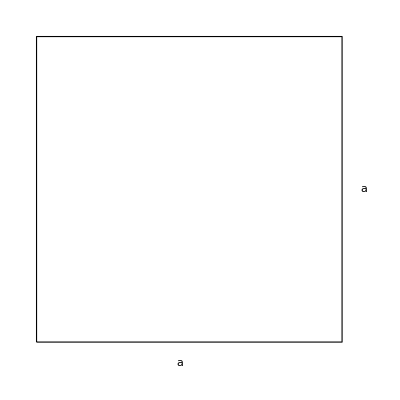

```mathematica
Graphics[{
Text[Style["a",Italic],#]&/@{{1.07,.5},{.47,-.07}},
White,EdgeForm[Black],Polygon[{{0,0},{1,0},{1,1},{0,1}}]
}]
```

## Diagonals

```mathematica
square=Quadrilateral@@RegularPolygon[4,1,Pi/4];
```

```mathematica
Show[Graphics[{
{
Red,
d=Diagonals[square],
PerpSquare[d,.05,1],
EqualSideTicksAboutMidpoint[#,1,.03,0]&/@d
},
{
Blue,
EqualAngleDivisionTicks[#,2,1,.1,.03,0]&/@Partition[square[[1]],3,1,1]
},
square
}],AspectRatio->Automatic]
```

⁃Graphics⁃

## Properties

```mathematica
TableForm[RegularPolygonInformation[4]//Simplify,TableDepth->2]
```

sides n | 4
vertex angle α {rad, degrees} | {π/2,90 °}
central angle β {rad, degrees} | {π/2,90 °}
inradius r | 1/2
circumradius R | 1/(√2)
area A | 1

## Properties

```mathematica
ineq[x_,y_]:=Max[Abs[x],Abs[y]]≤a/2
```

### Centroid

```mathematica
Assuming[a>0,Centroid[ineq,{x,y}]]
```

{0,0}

```mathematica
Assuming[a>0,RegionCentroid[Rectangle[{-1,-1}a/2,{1,1}a/2]]]
```

{0,0}

### Area

```mathematica
area=Assuming[a>0,Area[ineq,{x,y}]]
```

a^2

```mathematica
Assuming[a>0,Simplify@Integrate[1,{x,y}∈Rectangle[{-1,-1}a/2,{1,1}a/2]]]
```

a^2

### InertiaTensor

```mathematica
Assuming[a>0,AreaInertiaTensor[ineq,{x,y}]]
```

{{a^4/12,0},{0,a^4/12}}

### RadiiOfGyration

```mathematica
Assuming[a>0,FullSimplify[RadiiOfGyration[ineq[x,y],{x,y}]]]
```

{a/(2 √3),a/(2 √3)}

### GeneralizedDiameter

```mathematica
ineqs=And@@ineq@@@{{x1,y1},{x2,y2}}/.a->1
```

Max[Abs[x1],Abs[y1]]≤1/2&&Max[Abs[x2],Abs[y2]]≤1/2

```mathematica
Maximize[{(x1-x2)^2+(y1-y2)^2,ineqs},{x1,x2,y1,y2}]//Timing
```

...takes forever...

```mathematica
ineq[x_,y_]:=-a/2<=x<=a/2&&-a/2≤y≤a/2
```

```mathematica
ineqs=And@@ineq@@@{{x1,y1},{x2,y2}}/.a->1
```

-1/2≤x1≤1/2&&-1/2≤y1≤1/2&&-1/2≤x2≤1/2&&-1/2≤y2≤1/2

```mathematica
Maximize[{(x1-x2)^2+(y1-y2)^2,ineqs},{x1,x2,y1,y2}]//Timing
```

{0.057991,{2,{x1→-1/2,x2→1/2,y1→-1/2,y2→1/2}}}

## Inequality

```mathematica
<<Graphics`InequalityGraphics`
<<Utilities`Typesetting`
```

```mathematica
InequalityPlot[Abs[x]+Abs[y]<1,{x},{y}]
```

⁃Graphics⁃

```mathematica
#[{Sqrt[x^2+y^2],Abs[x]+Abs[y]==1},{x,y}]&/@{Maximize,Minimize}
```

{{1,{x→-1,y→0}},{1/(√2),{x→-1/2,y→-1/2}}}

```mathematica
InequalityPlot[Max[Abs[x],Abs[y]]<1,{x},{y}]
```

⁃Graphics⁃

```mathematica
#[{Sqrt[x^2+y^2],Max[Abs[x],Abs[y]]==1},{x,y}]&/@{Maximize,Minimize}
```

{{√2,{y→-1,x→-1}},{1,{y→0,x→-1}}}

```mathematica
Show[GraphicsArray[
Block[{$DisplayFunction=Identity},
InequalityPlot[#<1,{x},{y},Ticks->None,
PlotLabel->TraditionalForm[#<1]]&/@{Abs[x]+Abs[y],Max[Abs[x],Abs[y]]}
]]]
```

⁃GraphicsArray⁃

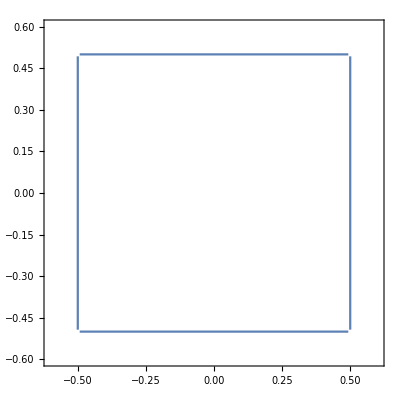

```mathematica
ContourPlot[Max[Abs[x],Abs[y]]==1/2,{x,-.6,.6},{y,-.6,.6}]
```

## Inscribed Square

```mathematica
v=Sqrt[2]Through[{Sin,Cos}[Pi(#+1/2)/2]]&/@Range[4];
v2=First[#]-.3Subtract@@#&/@Partition[v,2,1,1];
lines=Transpose[{RotateRight[v],v2}];
ineqs=Det[{{x,y,1},Append[First[#],1],Append[Last[#],1]}]<0&/@lines;
```

```mathematica
<<Graphics`InequalityGraphics`
<<Graphics`Colors`
```

```mathematica
Show[GraphicsArray[{
Graphics[{
ClosedLine[v],
InequalityPlot[And@@ineqs,{x},{y},DisplayFunction->Identity,Fills->Yellow][[1]],
Line/@lines
},AspectRatio->Automatic],
Graphics[{
ClosedLine[v],
Line/@lines
},AspectRatio->Automatic]}
]]
```

⁃GraphicsArray⁃